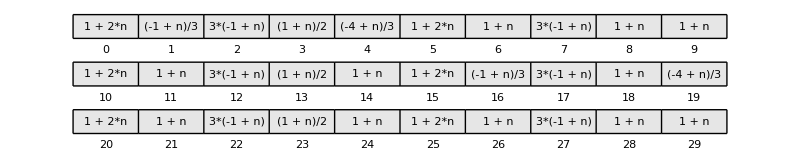

```mathematica
RMToAS[prog_,nr_]:=With[{p=Length[prog],g=∏_(j=1)^nr Prime[j]},{p g,Sort[Flatten[MapIndexed[With[{n=First[#2]-1},#1/.{i[r_]:>Table[n+j p->(Evaluate[Simplify[Prime[r] (#1-n)+n+1]]&),{j,0,g-1}],d[r_,k_]:>Table[n+j p->If[Mod[j,Prime[r]]==0,Evaluate[Simplify[(#1-n)/Prime[r]+k-1]]&,#1+1&],{j,0,g-1}]}]&,prog]]]}];

With[{rule=RMToAS[{{1},{2,1},{2},{1,3},{2,1}}/.{{a_}->i[a],{a_,b_}->d[a,b]},2]},Framed@GraphicsGrid[Riffle[Partition[ToString[#[n],InputForm]&/@Values[Last@rule],10],Partition[Keys[Last@rule],10]],Frame->{None,None,Flatten@Table[{j,i}->True,{i,10},{j,1,6,2}]},Background->{None,{{GrayLevel[.9],None}}},ImageSize->800,Spacings->{0,2}]]
```